```mathematica
HisDis[n_,numSamples_]:=Block[{samples=RandomReal[{-1,1},{numSamples,n}],lengths=Norm/@samples,filteredSamples},
filteredSamples=Select[samples,Norm[#]>1&];
Histogram[
Flatten[ParallelTable[Norm[filteredSamples[[i]]-filteredSamples[[j]]],{i,Length[filteredSamples]},{j,i+1,Length[filteredSamples]}]]
,20,"Probability",ChartLegends->{"Distances"},ChartLabels->{"Distance","Probability Density"}]
]
```

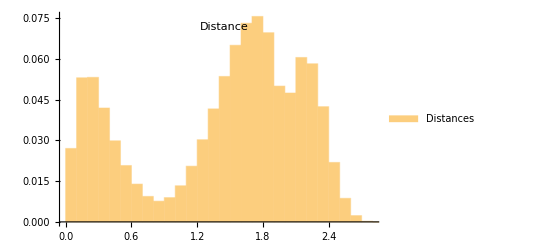

```mathematica
HisDis[2,50000]
```

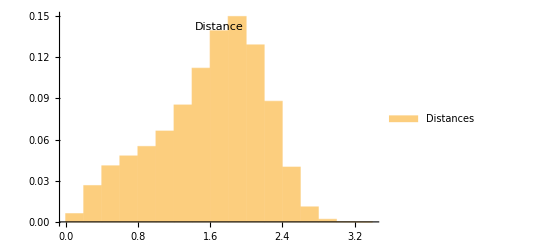

```mathematica
HisDis[3,20000]
```

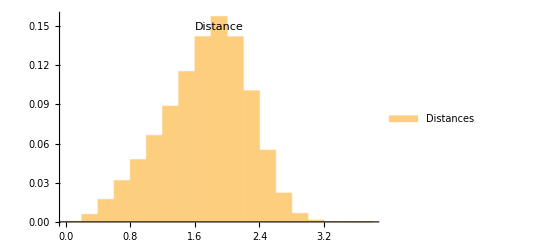

```mathematica
HisDis[4,20000]
```

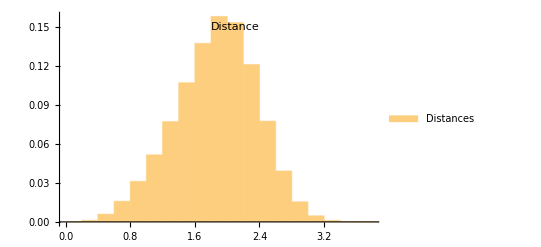

```mathematica
HisDis[5,20000]
```

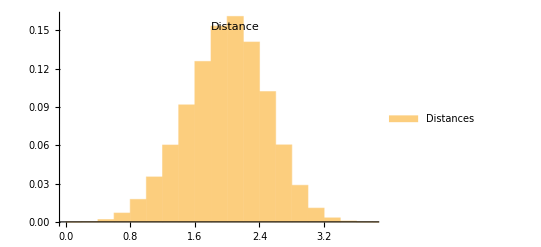

```mathematica
HisDis[6,15000]
```

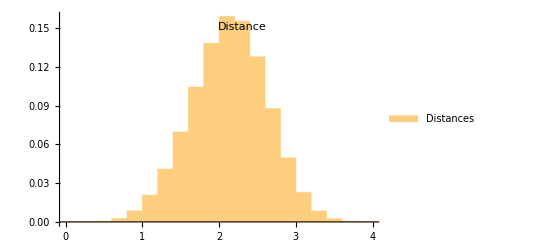

```mathematica
HisDis[7,15000]
```

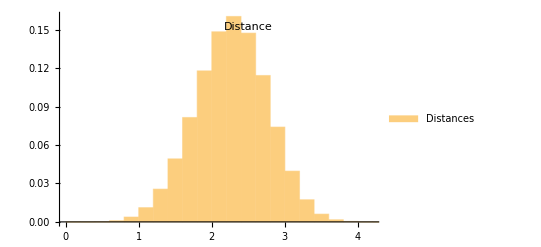

```mathematica
HisDis[8,15000]
```

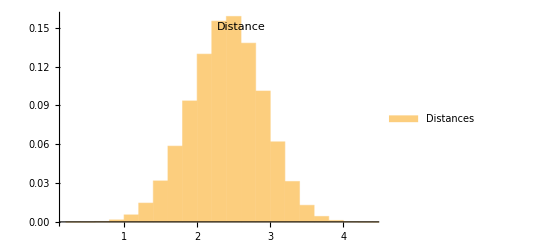

```mathematica
HisDis[9,15000]
```

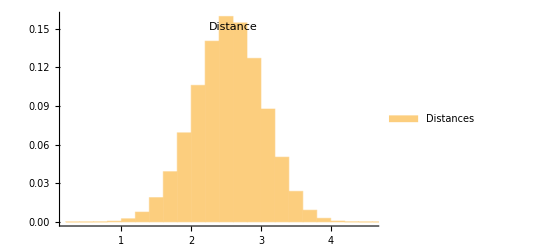

```mathematica
HisDis[10,15000]
```

```mathematica
imgs={%2,%3,%4,%5,%6,%7,%8,%9,%10}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
imgsR=Rasterize[#,ImageResolution->300,ImageSize->Medium]&/@imgs
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Export["D:\\wroot\\ManimWorks\\ANN\\images\\dis_"<>ToString[#+1]<>".png",imgsR[[#]]]&/@Range[1,9]
```

{D:\wroot\ManimWorks\ANN\images\dis_2.png,D:\wroot\ManimWorks\ANN\images\dis_3.png,D:\wroot\ManimWorks\ANN\images\dis_4.png,D:\wroot\ManimWorks\ANN\images\dis_5.png,D:\wroot\ManimWorks\ANN\images\dis_6.png,D:\wroot\ManimWorks\ANN\images\dis_7.png,D:\wroot\ManimWorks\ANN\images\dis_8.png,D:\wroot\ManimWorks\ANN\images\dis_9.png,D:\wroot\ManimWorks\ANN\images\dis_10.png}